```mathematica
Needs["AGT`",FileNameJoin[{NotebookDirectory[],"agt.m"}]]
```

```mathematica
GTSP[G1_,G2_]:=
Module[
{L1=KirchhoffMatrix[G1],L2=KirchhoffMatrix[G2],V,E},
V=
E=Table[
If[
Xor[EdgeQ[G1,v1<->v2],EdgeQ[G2,cond]]
UndirectedEdge[v1,v2]
]
,{v1,G1//VertexList},{v2,G2//VertexList}];
Graph[{V,E}]
]
```

```mathematica
l=5;
gg=GridGraph[{l,l}];
p1=PathGraph[Range[l]];
p2=PathGraph[Range[l]];

p1p2=DeleteCases[
Flatten[
Table[
If[
Or[
And[u==v,EdgeQ[p1,up<->vp]],
And[EdgeQ[p2,u<->v],up==vp]
],
{u,up}<->{v,vp}
],
{u,VertexList[p1]},
{up,VertexList[p1]},
{v,VertexList[p2]},
{vp,VertexList[p2]}
],
4
],
Null
]//Graph//SimpleGraph;

FindGraphIsomorphism[gg,p1p2]
```

{<|1→{1,1},2→{1,2},3→{1,3},4→{1,4},5→{1,5},6→{2,1},7→{2,2},8→{2,3},9→{2,4},10→{2,5},11→{3,1},12→{3,2},13→{3,3},14→{3,4},15→{3,5},16→{4,1},17→{4,2},18→{4,3},19→{4,4},20→{4,5},21→{5,1},22→{5,2},23→{5,3},24→{5,4},25→{5,5}|>}

```mathematica
Table[
{i,CycleGraph[i]//SmithSeq},
{i,3,6}
]//Column
```

{3,{1,3,0}}
{4,{1,1,4,0}}
{5,{1,1,1,5,0}}
{6,{1,1,1,1,6,0}}

```mathematica
Table[
{i,PathGraph[i//Range]//SmithSeq},
{i,3,6}
]//Column
```

{3,{1,1,0}}
{4,{1,1,1,0}}
{5,{1,1,1,1,0}}
{6,{1,1,1,1,1,0}}

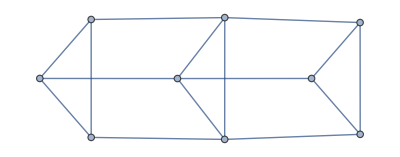
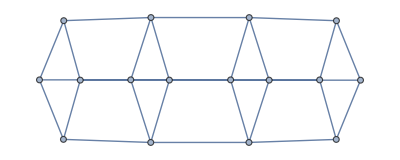
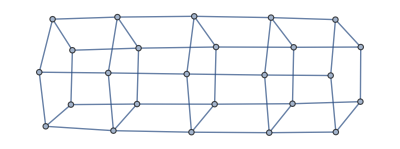
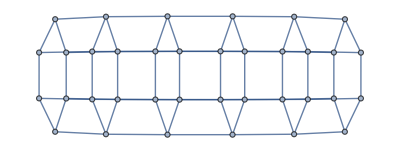
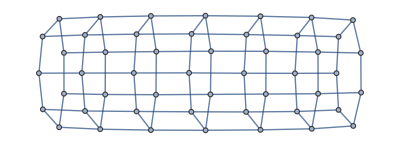
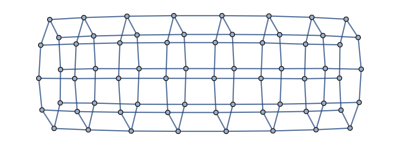
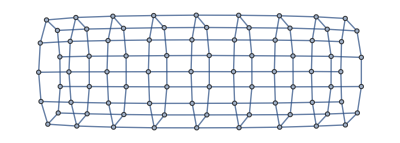
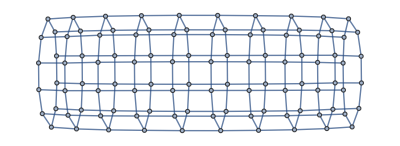
{{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
Table[
{i,GCartProd[PathGraph[Range[i]],CycleGraph[i]]},
{i,3,10}
]
```